```mathematica
SetDirectory[NotebookDirectory[]];
ClearAll["Global`*"]
fNegativeBinomialCustom[λ_,k_]:=Module[{n,p},p = k/(λ+k); n = (p λ)/(1-p); NegativeBinomialDistribution[n,p]]
fGeneratePoint[aMean_,aKappa_]:=RandomVariate[fNegativeBinomialCustom[aMean,aKappa],{1}][[1]]
fMean[N_,t_,λ_,ψ_]:=If[N ψ Exp[-λ t]>0.001,N ψ Exp[-λ t],0.001]
fMeans[N_,lT__,λ_,ψ_]:=Table[fMean[N,t,λ,ψ],{t,lT}]
fGenerateSeries[N_,lT__,λ_,ψ_,κ_]:=Module[{lMeans=fMeans[N,lT,λ,ψ]},fGeneratePoint[#,κ]&/@lMeans]
fLogLikelihood[y_,N_,t_,λ_,ψ_,κ_]:=LogLikelihood[fNegativeBinomialCustom[fMean[N,t,λ,ψ],κ],{y}]
fLogLikelihoodTotal[lY_,N_,lT_,λ_,ψ_,κ_]:=Total[fLogLikelihood[#1,N,#2,λ,ψ,κ]&@@@Thread[{lY,lT}]]
fMaximise[lY__,lT__,N_Integer]:=Module[{lMax,λ,κ,ψ},lMax=NMaximize[{fLogLikelihoodTotal[lY,N,lT,λ,ψ,κ],1>λ>0.01,1>ψ>0,50>κ>0.01},{λ,ψ,κ}][[2]];{lMax[[1,2]],lMax[[2,2]],lMax[[3,2]]}]
fLifetimeError[aLambdaTrue_,lY__,lT__,N_Integer]:=Module[{aLambdaEst=Quiet[fMaximise[lY,lT,N][[1]]]},(1/aLambdaTrue)-(1/aLambdaEst)]
fMCLifetimeError[λ_,ψ_,κ_,N_Integer,MaxT_]:=Module[{lY=fGenerateSeries[N,Range@MaxT,λ,ψ,κ]},fLifetimeError[λ,lY,Range@MaxT,N]]
fMCLifetimeErrorSD[numReplicates_Integer,λ_,ψ_,κ_,N_Integer,MaxT_]:=Module[{lErrors=Table[fMCLifetimeError[λ,ψ,κ,N,MaxT],{i,1,numReplicates,1}]},StandardDeviation@lErrors]
fMCLifetimeErrorRMSE[numReplicates_Integer,λ_,ψ_,κ_,N_Integer,MaxT_]:=Module[{lErrors=Table[fMCLifetimeError[λ,ψ,κ,N,MaxT],{i,1,numReplicates,1}]},lErrors]
```

## Vary T max = (6 to 25), N = 1300 (median from MRR database), ψ = 0.03 (median), κ = 3.18 (median). Medians from “exponential_species_sex_sugar_log_priors_justified.stan” model i.e. species level model including sex differences and feeding differences

```mathematica
lY=fGenerateSeries[1300,lt,1/5,0.03,3.18];
```

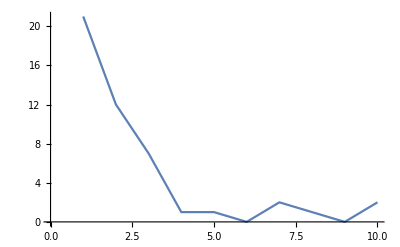

```mathematica
ListLinePlot[lY]
```

```mathematica
fMaximise[lY,lt,1300]
```

{0.241499,0.0586095,50.}

```mathematica
lMu = {1/5,1/10};
ψ = 0.03;
κ = 3.18;
n = 1300;
numReplicates =200;
lt=Table[t,{t,6,25,2}];
```

```mathematica
lRMSE1=Table[ParallelTable[{t,fMCLifetimeErrorRMSE[numReplicates,μ,ψ,κ,n,t]},{t,lt}],{μ,lMu}];
```

```mathematica
lower=Table[Quantile[#,0.25]&/@Abs[lRMSE1[[i,All,2]]],{i,1,Length@lMu,1}];
middle=Table[Quantile[#,0.5]&/@Abs[lRMSE1[[i,All,2]]],{i,1,Length@lMu,1}];
upper=Table[Quantile[#,0.75]&/@Abs[lRMSE1[[i,All,2]]],{i,1,Length@lMu,1}];
```

```mathematica
Export["power_duration_1.csv",lower]
Export["power_duration_2.csv",middle]
Export["power_duration_3.csv",upper]
Export["power_duration_t.csv",lt]
```

power_duration_1.csv

power_duration_2.csv

power_duration_3.csv

power_duration_t.csv

## Same but now vary sample size

```mathematica
lower=100;
upper=10000;
lN=10^Subdivide[Log10[lower],Log10[upper],10];
```

```mathematica
lRMSE2=Table[ParallelTable[{n,fMCLifetimeErrorRMSE[numReplicates,μ,ψ,κ,Round[n],12]},{n,lN}],{μ,lMu}];
```

```mathematica
lower=Table[Quantile[#,0.25]&/@Abs[lRMSE2[[i,All,2]]],{i,1,Length@lMu,1}];
middle=Table[Quantile[#,0.5]&/@Abs[lRMSE2[[i,All,2]]],{i,1,Length@lMu,1}];
upper=Table[Quantile[#,0.75]&/@Abs[lRMSE2[[i,All,2]]],{i,1,Length@lMu,1}];
```

```mathematica
Export["power_size_1.csv",lower]
Export["power_size_2.csv",middle]
Export["power_size_3.csv",upper]
Export["power_size_n.csv",Round/@lN]
```

power_size_1.csv

power_size_2.csv

power_size_3.csv

power_size_n.csv